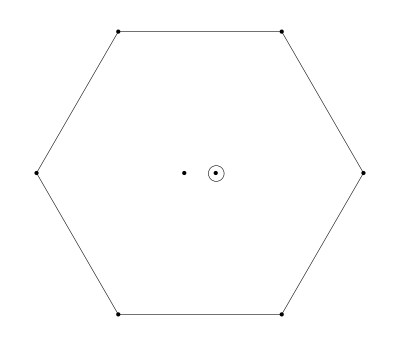

Y=0,  I_3=0

-4uuūū+8ddd̄d̄-4sss̄s̄-2(us+su)(ūs̄+s̄ū)+(sd+ds)(s̄d̄+d̄s̄)+(ud+du)(ūd̄+d̄ū)

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_a 1C((s̄)_b)^T)+(d_a^T C1 s_b+s_a^T C1 d_b) ((d̄)_b 1C((s̄)_a)^T)+(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_a 1C((d̄)_b)^T)+(d_a^T C1 s_b+s_a^T C1 d_b) ((s̄)_b 1C((d̄)_a)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_a 1C((ū)_b)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((d̄)_b 1C((ū)_a)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_a 1C((d̄)_b)^T)+(d_a^T C1 u_b+u_a^T C1 d_b) ((ū)_b 1C((d̄)_a)^T)+8 (d_a^T C1 d_b) ((d̄)_a 1C((d̄)_b)^T+(d̄)_b 1C((d̄)_a)^T)-2 (s_a^T C1 u_b+u_a^T C1 s_b) ((s̄)_a 1C((ū)_b)^T)-2 (s_a^T C1 u_b+u_a^T C1 s_b) ((s̄)_b 1C((ū)_a)^T)-2 (s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_a 1C((s̄)_b)^T)-2 (s_a^T C1 u_b+u_a^T C1 s_b) ((ū)_b 1C((s̄)_a)^T)-4 (s_a^T C1 s_b) ((s̄)_a 1C((s̄)_b)^T+(s̄)_b 1C((s̄)_a)^T)-4 (u_a^T C1 u_b) ((ū)_a 1C((ū)_b)^T+(ū)_b 1C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
4 (d̄(γ^μ).(γ̄)^5 d d̄(γ^μ).(γ̄)^5 d)+4 (d̄ γ^μ d d̄ γ^μ d)-4 (d̄(γ̄)^5 d d̄(γ̄)^5 d)+2 (d̄ σ^μν d d̄ σ^μν d)+d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s+d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d+d̄ γ^μ d s̄ γ^μ s+d̄ γ^μ s s̄ γ^μ d-d̄(γ̄)^5 s s̄(γ̄)^5 d+1/2 (d̄ σ^μν d s̄ σ^μν s)+1/2 (d̄ σ^μν s s̄ σ^μν d)+(s̄(γ̄)^5 s) (2 (ū(γ̄)^5 u)-d̄(γ̄)^5 d)+(s̄ 1s) (2 (ū 1u)-d̄ 1d)-d̄ 1s s̄ 1d+d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u+d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d+d̄ γ^μ d ū γ^μ u+d̄ γ^μ u ū γ^μ d-d̄(γ̄)^5 d ū(γ̄)^5 u-d̄(γ̄)^5 u ū(γ̄)^5 d+1/2 (d̄ σ^μν d ū σ^μν u)+1/2 (d̄ σ^μν u ū σ^μν d)-d̄ 1d ū 1u-d̄ 1u ū 1d-4 (d̄ 1d d̄ 1d)-2 (s̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 s)-2 (s̄ γ^μ s s̄ γ^μ s)+2 (s̄(γ̄)^5 s s̄(γ̄)^5 s)-s̄ σ^μν s s̄ σ^μν s-2 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)-2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)-2 (s̄ γ^μ s ū γ^μ u)-2 (s̄ γ^μ u ū γ^μ s)+2 (s̄(γ̄)^5 u ū(γ̄)^5 s)-s̄ σ^μν s ū σ^μν u-s̄ σ^μν u ū σ^μν s+2 (s̄ 1u ū 1s)+2 (s̄ 1s s̄ 1s)-2 (ū(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 u)-2 (ū γ^μ u ū γ^μ u)+2 (ū(γ̄)^5 u ū(γ̄)^5 u)-ū σ^μν u ū σ^μν u+2 (ū 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(64 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(16 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (49 m_d+m_s+m_u) q^4)/(3 π^4)-(⟨ s̄ s⟩ log(-q^2/μ^2) (2 m_d+29 m_s+8 m_u) q^4)/(6 π^4)-(⟨ ū u⟩ log(-q^2/μ^2) (2 m_d+8 m_s+29 m_u) q^4)/(6 π^4)-(4 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(10 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(10 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(144 π^6)-(12 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(131 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(12 π^2)-(13 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)-(13 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(36 π^2)-(31 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(24 π^2)+(103 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)-(13 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)+(103 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(72 π^2)-(31 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(24 π^2)-(164 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(50 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(50 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)+(1013 ⟨ d̄ Gd⟩^2)/(144 π^2 q^2)+(493 ⟨ s̄ Gs⟩^2)/(288 π^2 q^2)+(493 ⟨ ū Gu⟩^2)/(288 π^2 q^2)-(10 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)-(10 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)-(76 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(127 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(288 π^2 q^2)+(127 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(288 π^2 q^2)+(227 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(144 π^2 q^2)-(4 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (-4 m_d-104 m_s))/(9 q^2)-(4 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (184 m_d-4 m_s))/(9 q^2)-(4 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (-4 m_d-104 m_u))/(9 q^2)-(4 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (184 m_d-4 m_u))/(9 q^2)-(16 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (40 m_s-4 m_u))/(9 q^2)-(16 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (40 m_u-4 m_s))/(9 q^2)-(32 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (m_d-2 (m_s+m_u)))/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

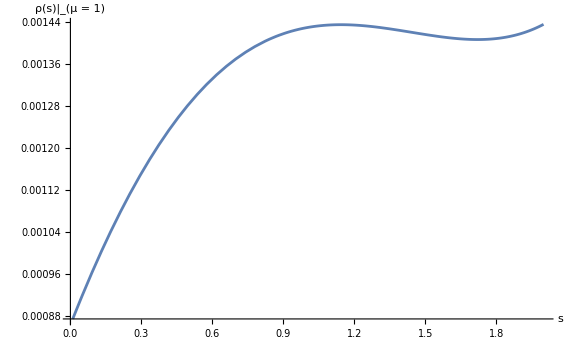
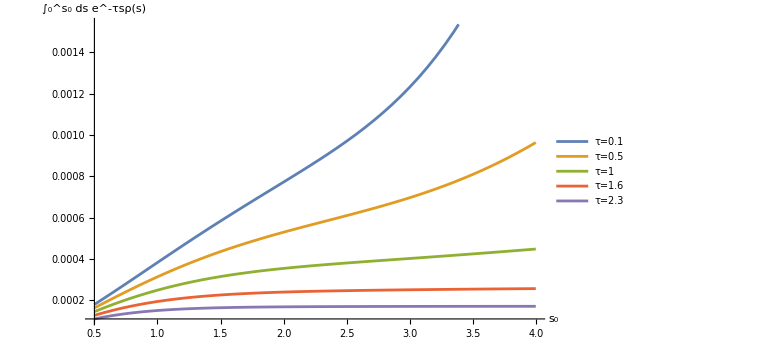

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

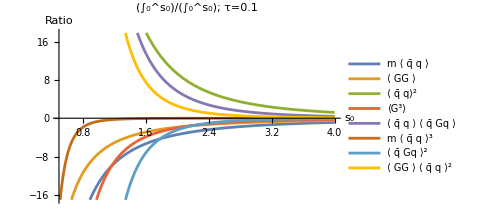
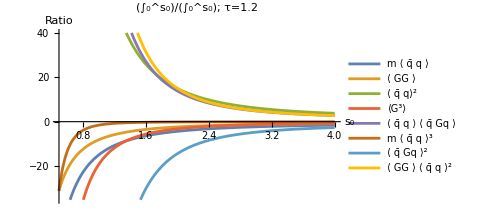
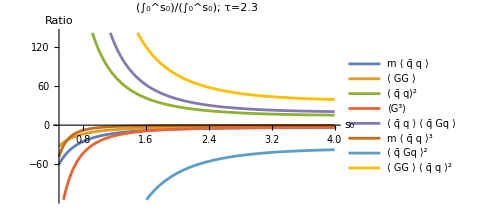

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

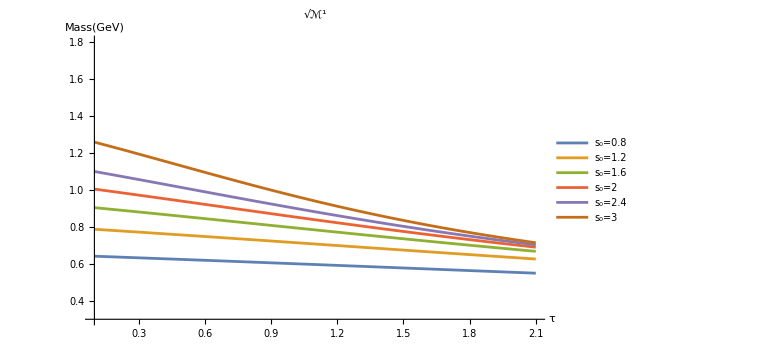
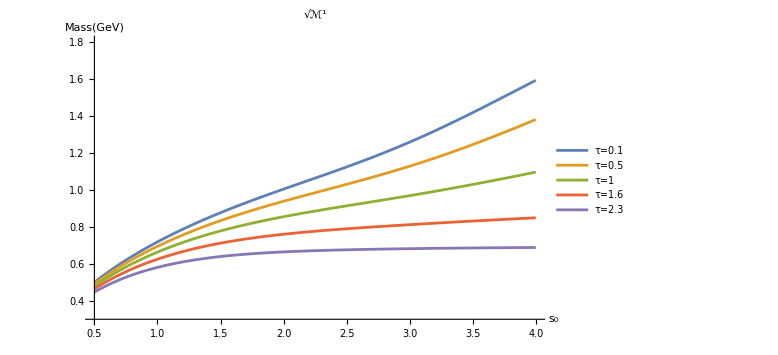

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

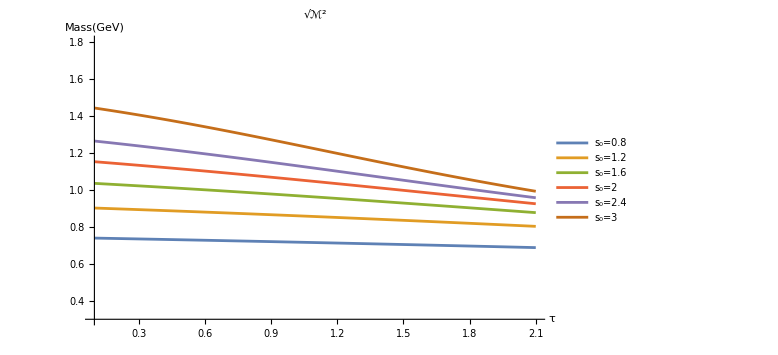
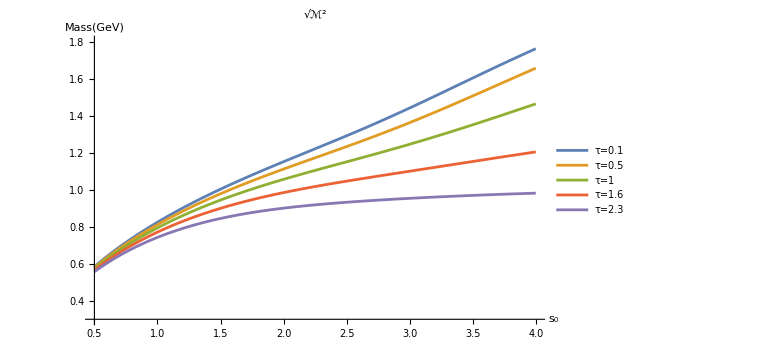

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

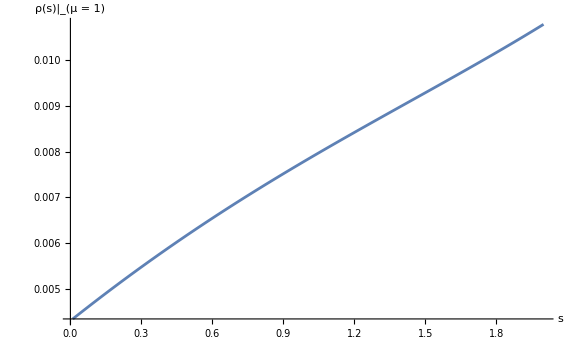
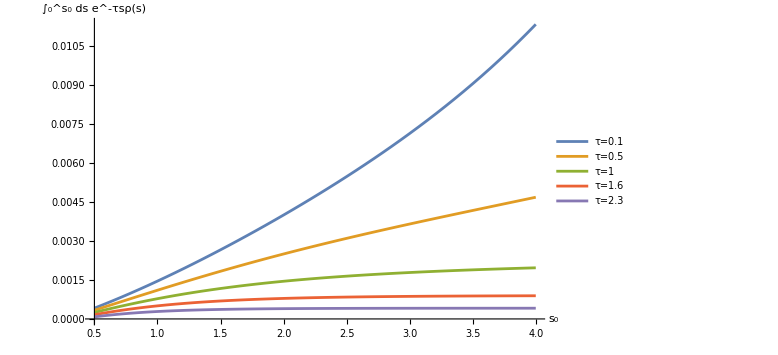

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

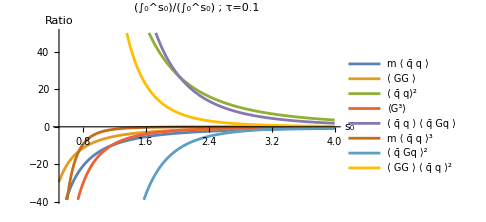
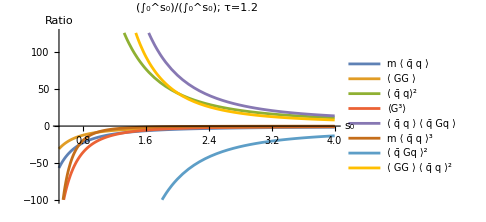
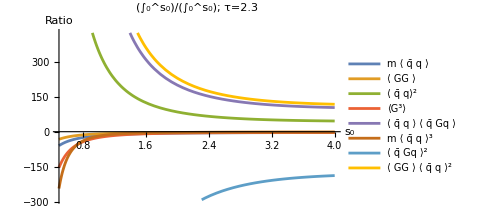

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

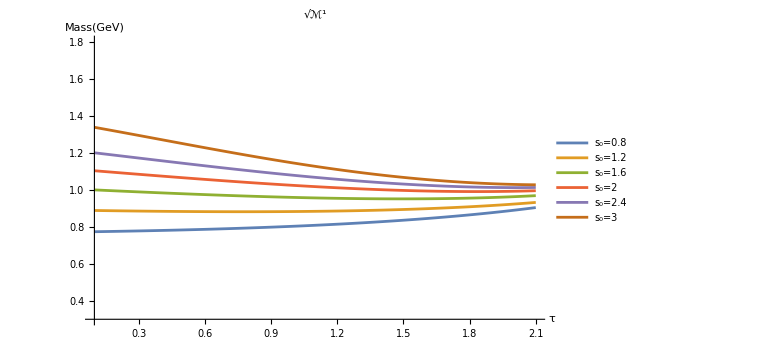
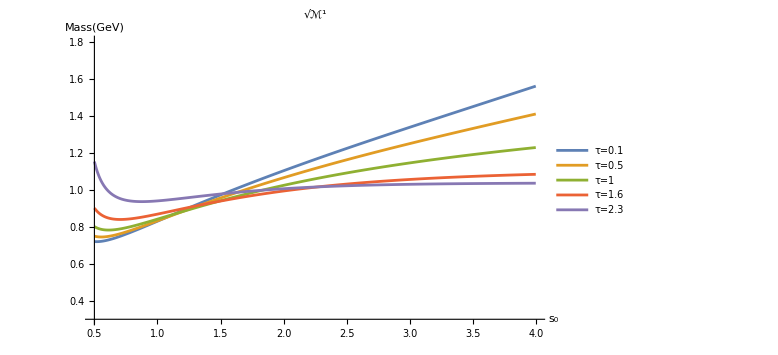

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5